```mathematica
(* Returns a Nested list of pair of points representing each line in polygon*)
lineList[list_]:=Partition[Append[list,First[list]],2,1];
```

```mathematica
(*Returns a Vector for a line between two points*)
vector[{{x1_,y1_},{x2_,y2_}}]:={x2-x1,y2-y1}
```

Reference : https : // demonstrations.wolfram.com/SegmentIntersection

```mathematica
(*The parametric equation of the line containing the points a and b is a+λ (b-a), where 0≤λ≤1 for points between a and b. The value of λ is given by*)λ[{a_,b_}][p_]:=((a-p).(a-b))/((a-b).(a-b))
```

```mathematica
(*for p on the line. For p not on the line, λ gives the closest point on the line.*)
(*Two lines, Subscript[L, 1] containing the points a and b with line Subscript[L, 2] containing the points c and d, intersect at a point ⟺ |{a-b,c-d}|≠0.  Compute the intersection point:*)
LineIntersectionPoint[{{a_,b_},{c_,d_}}]:=(Det[{a,b}] (c-d)-Det[{c,d}] (a-b))/Det[{a-b,c-d}]
```

```mathematica
(*Use |{a-b,c-d}|≠0 along with the condition 0≤λ≤1 to determine whether two segments intersect:*)
SegmentIntersectionQ[{p1:{a_,b_},p2:{c_,d_}}(*,endpoints_*)]:=
If[Det[{a-b,c-d}]==0,False,
Module[{p=Chop@LineIntersectionPoint[{p1,p2}]},
(*If[endpoints==False,*)(0≤  λ[p1][p]≤  1) &&(0≤  λ[p2][p]≤  1)&& Not@(p== a ||  p== b ||  p== c ||  p== d)(*,(0≤  λ[p1][p]≤  1) &&(0≤  λ[p2][p]≤  1)]*)  ]]
(*made a  change in the condition to ignore the end points i.e return false if p == end points and chop@p*)
```

```mathematica
(* Returns the angle made in [o,2Pi) Range*)
(*Reference: https://mathematica.stackexchange.com/questions/111629/calculating-the-angle-between-the-line-joining-two-points-and-the-x-axis*)
getAngle[{{x1_,y1_},{x2_,y2_}}]:=Mod[ArcTan[x2-x1,y2-y1],2 π]
```

```mathematica
vertexList[list_]:=Partition[Join[list,list⟦1;;2⟧],3,1]
```

```mathematica
(*true if pt  is inside polygon*)
testpoint[poly_,pt_]:=Round[(Total@Mod[(#-RotateRight[#])&@(ArcTan@@(pt-#)&/@poly),2 Pi,-Pi]/2/Pi)]≠0
```

```mathematica
glancingBlow[a_,{p1_,p2_,p3_}]:=
Xor[reflex[p1,p2,a], reflex[p3,p2,a]]
```

```mathematica
(*Function Gives whether a point is reflex or not, Chop is used to round of to the nearest integer. From Motion Plannning Book by Steven M.LaValle*)
reflex[{x1_,y1_},{x2_,y2_},{x3_,y3_}]:=Chop[Det[({{1, x1, y1}, {1, x2, y2}, {1, x3, y3}})]>0]
```

```mathematica
Manipulate[Module[{o,boundpoly,poly1,poly2,listofAllLines,sortedList,sortedText,jList={},InfinteLine,i,visibleList={},wi,wip,oldO={},oldP={},tempList={},p=pts⟦13⟧,glanceLine,glanceLineList={},intersectGlancePoint={},intersectGlancePointList={},finalBound,visiblePoly,visibleListwithline={},preGlancingPointQ=False,glancingBlowQ=False},
(*Obstacle Centroids*)
o={pts⟦11⟧,pts⟦12⟧};

(*Obstacle and Boundary Polygon Points*)
boundpoly=pts⟦1;;10⟧;
finalBound=8CirclePoints@4;
poly1=(o⟦1⟧+#)&/@(CirclePoints@6);
poly2=(o⟦2⟧+#)&/@(CirclePoints@4);

(*List of all lines in space*)
If[oldO ≠ o ||oldP≠ p,
oldO=o;
oldP=p;

listofAllLines=Join[lineList@finalBound,lineList@(boundpoly),lineList@(poly1),lineList@(poly2)];
(*Line Parallel to X axis*)
InfinteLine={p,{0.1,0}+{Max@(#⟦1⟧&/@(Join[finalBound,boundpoly,poly1,poly2])),p⟦2⟧}};

(*Find if Point lies in any of the polygon then reverse the list reresenting that polygon*)
If[testpoint[poly1,p],poly1=Reverse@poly1];
If[testpoint[poly2,p],poly2=Reverse@poly2];
If[testpoint[boundpoly,p],boundpoly=Reverse@boundpoly];
If[testpoint[finalBound,p],finalBound=Reverse@finalBound];

(*Sort the lines based on the angle w.r.t to point p*)
sortedList=N@Sort[Join[vertexList@(finalBound),vertexList@(boundpoly),vertexList@poly1,vertexList@poly2],If[getAngle[{p,#1⟦2⟧}]≠  getAngle[{p,#2⟦2⟧}],getAngle[{p,#1⟦2⟧}]<getAngle[{p,#2⟦2⟧}],Norm[p-#1⟦2⟧]<Norm[p-#2⟦2⟧]] &];

(*get the intersection of lines for the Infinteline*)
If[SegmentIntersectionQ[{InfinteLine,#}],AppendTo[jList,#]]&/@listofAllLines;

(*Store the sorted values in J list*)
SortBy[jList,EuclideanDistance[LineIntersectionPoint[Chop@{InfinteLine,#}],p]<EuclideanDistance[LineIntersectionPoint[Chop@{InfinteLine,#}],p]&];
AppendTo[visibleListwithline,Last@jList];

(*Loop around all the w's*)
For[i=1,i≤ Length@sortedList,i++,
If[intersectInteriorQRev2[p,sortedList⟦i⟧],wi=False,If[i==1 ||Not@pointOnSegmentQ[{p,sortedList⟦i,2⟧},sortedList⟦i,1⟧],If[Or@@((SegmentIntersectionQ[{{p,sortedList⟦i,2⟧},#}])&/@jList),wi=False,wi=True],If[Not@wip,wi=False,If[Or@@(SegmentIntersectionQ[{{sortedList⟦i,1⟧,sortedList⟦i,2⟧}},False])&/@jList,wi=False,wi=True]]]];

(*visible condition*)
If[wi,
(*Glancing blow Condition*)
If[Not@glancingBlow[p,sortedList⟦i⟧],glancingBlowQ=True;
glanceLine=extendedLine[p,sortedList⟦i,2⟧];
intersectGlancePoint = Sort[(DeleteCases[(If[SegmentIntersectionQ[{glanceLine,#}],LineIntersectionPoint[{glanceLine,#}]]&/@jList),Null]),EuclideanDistance[p,#1]< EuclideanDistance[p,#2]&]⟦1⟧;

(*Codition to decide the order of appending*)
If[(And[glancingBlowQ,preGlancingPointQ])||(pointOnSegmentQ[Last@visibleListwithline,intersectGlancePoint]),
AppendTo[visibleList,intersectGlancePoint];
AppendTo[visibleList,sortedList⟦i,2⟧]
,AppendTo[visibleList,sortedList⟦i,2⟧];AppendTo[visibleList,intersectGlancePoint]];
(*END the order if statement*)

AppendTo[intersectGlancePointList,intersectGlancePoint];AppendTo[glanceLineList,glanceLine]
,AppendTo[visibleList,sortedList⟦i,2⟧];
glancingBlowQ=False];
(*End Glancing blow Condition*)

AppendTo[visibleListwithline,sortedList⟦i,1;;2⟧]
];
(*END the visible condition*)
(*Print@i;
Print@preGlancingPointQ;
Print@glancingBlowQ;*)
preGlancingPointQ=glancingBlowQ;
wip=wi;
AppendTo[jList,{sortedList⟦i,1⟧,sortedList⟦i,2⟧}];
jList=DeleteDuplicates@jList;
jList=DeleteCases[jList,{sortedList⟦i,2⟧,sortedList⟦i,3⟧}];
AppendTo[tempList,jList]
];
];

(*Number Text to the Sorted Lines*)
sortedText=Table[Text[i,{0,0}+Mean@{p,sortedList⟦i,2⟧}],{i,1,Length@sortedList,1}];

m=Length@sortedList;
(*AppendTo[visibleList,First@visibleList];
visiblePoly = Table[{p,visibleList⟦i⟧,visibleList⟦i+1⟧},{i,1,Length@visibleList-1,1}];
Print@visiblePoly;*)

Graphics[{
(*Boundary Polygon*)
{{White,Polygon@finalBound}}
,{{(*EdgeForm[{Thin,Gray}],*)LightYellow,Polygon@(visibleList)(*Polygon@visiblePoly*)}}
,{{EdgeForm[Thin],Opacity[0],White,Polygon@boundpoly}}
,{{Blue,PointSize->Large,Point@p}}
(*Obstacle Polygons*)
,{{EdgeForm[Thin],Opacity[0.1],White,Polygon@poly1}}
,{{EdgeForm[Thin],Opacity[0.1],White,Polygon@poly2}}
(*Lines from point P and point P*)
(*,{{Opacity[0.2],Blue,Line@(*({p,#⟦2⟧})&/@*){p,sortedList⟦s,2⟧}}}
,{{Blue,sortedText⟦s⟧}}*)
(*Infinite Line*)
(*,{{Blue,Line@InfinteLine}}*)
(*,{{Green,Line@tempList⟦s⟧}}*)
,{{Red,Point@visibleList}}
(*,{{Purple,Line@glanceLineList}}*)
,(*{{Orange,Line@{{-0.5,-0.8660254037844386},{0.5,-0.8660254037844386}}}}*)
,{{Blue,Point@intersectGlancePointList}}
(*,{{Green,Line@visibleListwithline}}*)
}]
]
,{{s,1,"Slider"},1,m,1}
,{{m,1},ControlType-> None}
,{{pts,{{0.5,5},{-4.3,2.6500000000000004},{-5,-0.16999999999999993},{-5,-3.},{3.5,-5},{0,-2.5},{1.25,0},{4.25,0},{0.5,1.1500000000000001},{-1.1500000000000001,0.75},{0,0},{2,2},{-2.785,-2.84},{0,0},{2,2},{-2.785,-2.84}}}
,5{-1,-1},5{1,1},Locator,Appearance->None}
]
```

```mathematica
pointOnSegmentQ[{{x1_,y1_},{x2_,y2_}},{x3_,y3_}]:=Module[{ABv ={x2-x1,y2-y1,0},ACv={x3-x1,y3-y1,0},Kac,Kab},
If[And@@((Chop@#==0)&/@Cross[ABv,ACv]),
Kac=(ABv.ACv);
Kab=(ABv.ABv);
If[Kac<0,False,
If[Kac>Kab,False,
If[0<Kac<Kab,True,False]
]],False]]
```

```mathematica
(*True if w2 is Interior vertex from p *)
intersectInteriorQRev2[p_,{w1_,w2_,w3_}]:=getClockwiseAngle[w1,w2,w3]> getClockwiseAngle[p,w2,w3]
(*Clockwise angle bwtween tw o vectors*)
(*https://adndevblog.typepad.com/manufacturing/2012/07/finding-the-angle-between-two-vectors-along-a-given-direction-anti-clockwise-or-clockwise.html*)
getClockwiseAngle[p1_,p2_,p3_]:=Module[{a=p3-p2,b=p1-p2},
AppendTo[a,0];AppendTo[b,0];
If[Cross[a,b]⟦3⟧<0,(2Pi -VectorAngle[a,b]),VectorAngle[a,b]]
]
(*Returns if the vertex is not visible from point p *)
intersectInteriorQ[p_,{w1_,w2_,w3_}]:=Or[anglePoints[w1,w2,w3]< anglePoints[p,w2,w3],anglePoints[w1,w2,w3]< anglePoints[p,w2,w1]]
(*Returns angle between the three points*)
anglePoints[p0_,p1_,p2_]:=
Module[{a=((p1⟦1⟧-p0⟦1⟧)^2+(p1⟦2⟧-p0⟦2⟧)^2),b=((p1⟦1⟧-p2⟦1⟧)^2+(p1⟦2⟧-p2⟦2⟧)^2),c=((p2⟦1⟧-p0⟦1⟧)^2+(p2⟦2⟧-p0⟦2⟧)^2)},Mod[(ArcCos@((a+b-c)/Sqrt[4*a*b])),2Pi]]
```

```mathematica
extendedLine[p1_,p2_]:={p1,(p1+12Normalize@(p2-p1))}
```

```mathematica
getVectorQuadrantRev1[v1_,v2_]:=Module[{angle=getAngle[{v1,v2}]-( Pi/4),quadrant},
quadrant=((angle/(Pi/2)))+1;
If[quadrant< 0,quadrant+=4];
quadrant
]
```

```mathematica
Clear["Global`*"]
```

True

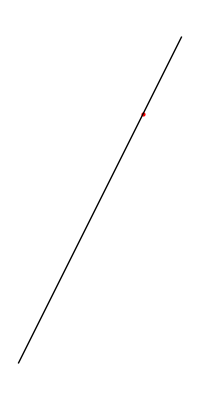

```mathematica
ip={0.9531320794818211,-0.5937358410363577};
lps=(*{{-0.5,-0.8660254037844386},{0.5,-0.8660254037844386}}*){{1.25,0.},{0.,-2.5}};
pointOnSegmentQ[lps,ip]
Graphics[{{Red,Point@ip},{Line@lps}}]
```